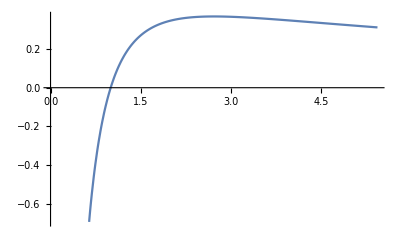

```mathematica
Plot[Log[x]/x,{x,0,2E}]
```

```mathematica
D[Log[x]/x,x]
```

1/x^2-Log[x]/x^2

```mathematica
N[(E-2)Log[E-2]/E]
```

-0.0874356

```mathematica
1-(E-2)Log[E-2]/E//FullSimplify
```

1-((-2+ⅇ) Log[-2+ⅇ])/ⅇ

```mathematica
Total[-# Log[#]&/@(#/Total[#])]&@{1,1,x-2}
```

-(2 Log[1/x])/x-((-2+x) Log[(-2+x)/x])/x

```mathematica
%//FullSimplify
```

-(2 Log[1/x]+(-2+x) Log[(-2+x)/x])/x

```mathematica
Solve[2 Log[1/x]+(-2+x) Log[(-2+x)/x]==-x,x,Reals]
```

{{x→Root[{Log[-2+#1] (-2+#1)+#1-Log[#1] #1&,2.3230146299843076464}]},{x→Root[{Log[-2+#1] (-2+#1)+#1-Log[#1] #1&,4.4450526810148322906}]}}

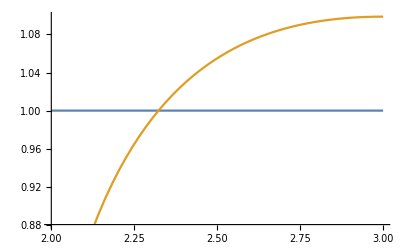

```mathematica
Plot[{1,-(2 Log[1/x]+(-2+x) Log[(-2+x)/x])/x},{x,2,3}]
```

```mathematica
Log[3]//N
```

1.09861

```mathematica
Root[{Log[-2+#1] (-2+#1)+#1-Log[#1] #1&,2.32301462998430764635112502218593569236`20.303815130457853}]//FullSimplify
```

Root[{Log[-2+#1] (-2+#1)+#1-Log[#1] #1&,2.3230146299843076464}]

```mathematica
D[Log[x]/(x+1),x]
```

1/(x (1+x))-Log[x]/(1+x)^2

```mathematica
Solve[%==0]
```

{{x→1/ProductLog[1/ⅇ]}}

```mathematica
1/ProductLog[1/ⅇ]//N
```

3.59112

```mathematica
Log[5]/6.
```

0.26824

```mathematica
Log[4]/5.
```

0.277259

```mathematica
Log[3]/4.
```

0.274653

```mathematica
?IntegerDigits
```

IntegerDigits[n] gives a list of the decimal digits in the integer n. 
IntegerDigits[n,b] gives a list of the base b digits in the integer n. 
IntegerDigits[n,b,len] pads the list on the left with zeros to give a list of length len. 
IntegerDigits[n,MixedRadix[blist]] uses the mixed radix with list of bases blist.

```mathematica
BaseForm[N@Pi,2.3]
```

BaseForm[3.14159,2.3]